```mathematica
Quit[];
```

## Load packages

```mathematica
$LoadFeynArts=True;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose = 0;

FAPatch[PatchModelsOnly->True];
```

Optional::opdef: The default value for the optional argument TraditionalForm`cc1_ : DiracGamma(h : 6 | 7)\ cc2_. contains a pattern.

General::stop: Further output of Optional :: opdef will be suppressed during this calculation.

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Patching FeynArts models... done!

# Compute ℳ_(K_L→ π^+e^-ν_e)

## Diagram and amplitude utilities (run this)

### Functions for generating diagrams

```mathematica
exclusions={V[1]};

model={"EFT_MeV_DM/EFT_MeV_DM"};
genericModel={"Lorentz","EFT_MeV_DM/EFT_MeV_DM"};

insertionLevel={Particles};
```

```mathematica
genDiags[inFields_,outFields_,nLoops_:0,adj_:{3}]:=Block[{tops},
tops=CreateTopologies[nLoops, Length[inFields]-> Length[outFields],ExcludeTopologies-> {Tadpoles,SelfEnergies,WFCorrections},Adjacencies-> adj];
InsertFields[tops,inFields-> outFields,InsertionLevel-> insertionLevel,Model-> model,GenericModel-> genericModel,ExcludeParticles-> exclusions]
]
```

```mathematica
paintDiags[diags_]:=Paint[diags,ColumnsXRows-> {Length[diags],1},SheetHeader->None,ImageSize-> {Length[diags]150,150}];
```

## Non-Radiative

```mathematica
ClearScalarProducts[];
```

```mathematica
SP[P,P]=mk0^2;
SP[p,p]=mpi^2;
SP[k,k]=0;
SP[q1,q1]=ml^2;
SP[q2,q2]=0;
```

### Compute Amplitudes

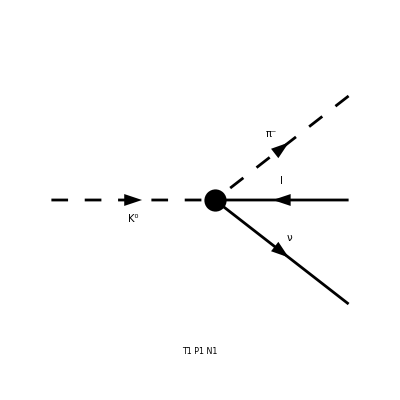

-√2 GF Vus ((φ(OverBar[q2])).(γ̄·p̄).(γ̄)^7.(φ(-OverBar[q1],ml))+(φ(OverBar[q2])).(γ̄·P̄).(γ̄)^7.(φ(-OverBar[q1],ml)))

```mathematica
diagsTree = genDiags[{S[3]}, {S[2],-F[2],F[1]},0,{3,4,5}];

Paint[diagsTree];

CreateFeynAmp[diagsTree,PreFactor-> -I];

FCFAConvert[%,IncomingMomenta-> {P},OutgoingMomenta-> {p, q1,q2},LorentzIndexNames->{μ},List-> False,UndoChiralSplittings-> True,ChangeDimension-> 4,FinalSubstitutions-> M$FACouplings];

(*Simplify[DiracSimplify[#,DiracSubstitute67-> True]]&/@%;*)
AmpK0Tree=%//PropagatorDenominatorExplicit//Calc//Simplify
```

## Radiative

```mathematica
ClearScalarProducts[];
```

```mathematica
SP[P,P]=mk0^2;
SP[p,p]=mpi^2;
SP[k,k]=0;
SP[q1,q1]=ml^2;
SP[q2,q2]=0;
```

### Compute Amplitudes

```mathematica
diags = genDiags[{S[3]}, {S[2],-F[2],F[1],V[1]},0,{3,4,5}];

(*Paint[diags,ColumnsXRows-> {2,1}];*)

CreateFeynAmp[diags,PreFactor-> -I];

FCFAConvert[%,IncomingMomenta-> {P},OutgoingMomenta-> {p, q1,q2,k},LorentzIndexNames->{μ},List-> True,UndoChiralSplittings-> True,ChangeDimension-> 4,FinalSubstitutions-> M$FACouplings,TransversePolarizationVectors->{k}];

Simplify[DiracSimplify[#,DiracSubstitute67-> True]]&/@%;
AmpK0List=%//PropagatorDenominatorExplicit//Simplify;
AmpK0List={AmpK0List⟦1⟧,AmpK0List⟦2⟧,-AmpK0List⟦3⟧};
AmpK0=AmpK0List//Total//Simplify;
```

### Check transversality

```mathematica
AmpK0/.Momentum[Polarization[k,-ⅈ]]->Momentum[k]/.P->p+k+q1+q2//DiracGammaCombine//Simplify
```

1/(2 √2)GF qe Vus (1/(k̄·p̄)2 (p̄·(ε̄)^*(k)) ((φ(OverBar[q2])).(γ̄·(k̄+p̄+OverBar[q1]+OverBar[q2])).(φ(-OverBar[q1],ml))-(φ(OverBar[q2])).(γ̄·(k̄+p̄+OverBar[q1]+OverBar[q2])).(γ̄)^5.(φ(-OverBar[q1],ml))+(φ(OverBar[q2])).(γ̄·k̄).(φ(-OverBar[q1],ml))-(φ(OverBar[q2])).(γ̄·k̄).(γ̄)^5.(φ(-OverBar[q1],ml))+(φ(OverBar[q2])).(γ̄·p̄).(φ(-OverBar[q1],ml))-(φ(OverBar[q2])).(γ̄·p̄).(γ̄)^5.(φ(-OverBar[q1],ml)))+1/(k̄·OverBar[q1])(-2 (OverBar[q1]·(ε̄)^*(k)) (φ(OverBar[q2])).(γ̄·p̄).(φ(-OverBar[q1],ml))-2 (OverBar[q1]·(ε̄)^*(k)) (φ(OverBar[q2])).(γ̄·(k̄+p̄+OverBar[q1]+OverBar[q2])).(φ(-OverBar[q1],ml))+2 (OverBar[q1]·(ε̄)^*(k)) (φ(OverBar[q2])).(γ̄·p̄).(γ̄)^5.(φ(-OverBar[q1],ml))+2 (OverBar[q1]·(ε̄)^*(k)) (φ(OverBar[q2])).(γ̄·(k̄+p̄+OverBar[q1]+OverBar[q2])).(γ̄)^5.(φ(-OverBar[q1],ml))-(φ(OverBar[q2])).(γ̄·p̄).(γ̄·k̄).(γ̄·(ε̄)^*(k)).(φ(-OverBar[q1],ml))-(φ(OverBar[q2])).(γ̄·(k̄+p̄+OverBar[q1]+OverBar[q2])).(γ̄·k̄).(γ̄·(ε̄)^*(k)).(φ(-OverBar[q1],ml))+(φ(OverBar[q2])).(γ̄·p̄).(γ̄·k̄).(γ̄·(ε̄)^*(k)).(γ̄)^5.(φ(-OverBar[q1],ml))+(φ(OverBar[q2])).(γ̄·(k̄+p̄+OverBar[q1]+OverBar[q2])).(γ̄·k̄).(γ̄·(ε̄)^*(k)).(γ̄)^5.(φ(-OverBar[q1],ml)))+2 ((φ(OverBar[q2])).(γ̄·(ε̄)^*(k)).(γ̄)^5.(φ(-OverBar[q1],ml))-(φ(OverBar[q2])).(γ̄·(ε̄)^*(k)).(φ(-OverBar[q1],ml))))

### Antiparticle amplitude

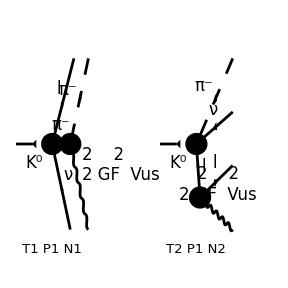

-1/2 ⅈ GF qe Vus ((2 (OverBar[Pl]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Pk]).(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Pl])^2-ml^2)-(2 (OverBar[Pl]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Pk]).(γ̄)^5.(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Pl])^2-ml^2)+((φ(OverBar[Pl],ml)).(γ̄·(ε̄)^*(Pg)).(γ̄·OverBar[Pg]).(γ̄·OverBar[Pk]).(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Pl])^2-ml^2)-((φ(OverBar[Pl],ml)).(γ̄·(ε̄)^*(Pg)).(γ̄·OverBar[Pg]).(γ̄·OverBar[Pk]).(γ̄)^5.(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Pl])^2-ml^2)+(2 (OverBar[Pl]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Ppi]).(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Pl])^2-ml^2)-(2 (OverBar[Pl]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Ppi]).(γ̄)^5.(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Pl])^2-ml^2)+((φ(OverBar[Pl],ml)).(γ̄·(ε̄)^*(Pg)).(γ̄·OverBar[Pg]).(γ̄·OverBar[Ppi]).(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Pl])^2-ml^2)-((φ(OverBar[Pl],ml)).(γ̄·(ε̄)^*(Pg)).(γ̄·OverBar[Pg]).(γ̄·OverBar[Ppi]).(γ̄)^5.(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Pl])^2-ml^2)+(((OverBar[Pg]+OverBar[Ppi])·(ε̄)^*(Pg)+OverBar[Ppi]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Pk]).(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Ppi])^2-mpi^2)-(((OverBar[Pg]+OverBar[Ppi])·(ε̄)^*(Pg)+OverBar[Ppi]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Pk]).(γ̄)^5.(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Ppi])^2-mpi^2)+(((OverBar[Pg]+OverBar[Ppi])·(ε̄)^*(Pg)+OverBar[Ppi]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Pg]).(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Ppi])^2-mpi^2)+(((OverBar[Pg]+OverBar[Ppi])·(ε̄)^*(Pg)+OverBar[Ppi]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Ppi]).(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Ppi])^2-mpi^2)-(((OverBar[Pg]+OverBar[Ppi])·(ε̄)^*(Pg)+OverBar[Ppi]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Pg]).(γ̄)^5.(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Ppi])^2-mpi^2)-(((OverBar[Pg]+OverBar[Ppi])·(ε̄)^*(Pg)+OverBar[Ppi]·(ε̄)^*(Pg)) (φ(OverBar[Pl],ml)).(γ̄·OverBar[Ppi]).(γ̄)^5.(φ(-OverBar[Pv])))/((-OverBar[Pg]-OverBar[Ppi])^2-mpi^2))

```mathematica
diags = genDiags[{-S[3]}, {-S[2],F[2],-F[1],V[1]},0,{3,4}];
Paint[diags,ColumnsXRows-> {2,1}];
CreateFeynAmp[diags,PreFactor-> -I];
FCFAConvert[%,IncomingMomenta-> {Pk},OutgoingMomenta-> {Ppi, Pl,Pv,Pg},List-> False,UndoChiralSplittings-> True,ChangeDimension-> 4,FinalSubstitutions-> M$FACouplings];
AmpK0Bar=%//DiracSimplify[#,DiracSubstitute67-> True]&//Simplify
```

### Compute Msqrd Using DoPolarizationSums

```mathematica
MsqrdK0=FCRenameDummyIndices[ComplexConjugate[AmpK0]]AmpK0//FermionSpinSum//
ReplaceAll[#,{DiracTrace-> Tr}]&//DoPolarizationSums[#,Pg,0]&//PropagatorDenominatorExplicit//Simplify;
```

```mathematica
MsqrdK0Bar=FCRenameDummyIndices[ComplexConjugate[AmpK0Bar]]AmpK0Bar//FermionSpinSum//ReplaceAll[#,{DiracTrace-> Tr}]&//DoPolarizationSums[#,Pg,0]&//PropagatorDenominatorExplicit//ReplaceAll[#,D-> 4]&//Simplify;
```

```mathematica
Msqrd=1/2(MsqrdK0+MsqrdK0Bar)//FullSimplify;
```

### Compute Msqrd Not using DoPolarizationSums

```mathematica
AmpK0UC=AmpK0//ReplaceAll[#,{Pair[Momentum[Polarization[Pg,-I]],a_]:>Pair[a,LorentzIndex[μ]],DiracGamma[Momentum[Polarization[Pg,-I]]]:> GA[μ]}]&;

AmpK0UCConj=AmpK0UC//ComplexConjugate//ReplaceAll[#,μ-> ν]&;
```

```mathematica
MsqrdK02=-MT[μ,ν]AmpK0UC AmpK0UCConj//FermionSpinSum//ReplaceAll[#,DiracTrace-> Tr]&//Contract//PropagatorDenominatorExplicit//Simplify
```

1/((OverBar[Pg]·OverBar[Pl])^2 (OverBar[Pg]·OverBar[Ppi])^2)2 GF^2 qe^2 Vus^2 (-(2 (mpi^2+OverBar[Pg]·OverBar[Ppi]) (OverBar[Pg]·OverBar[Pv])+(2 mpi^2+3 (OverBar[Pg]·OverBar[Ppi])) (OverBar[Pk]·OverBar[Pv]+OverBar[Ppi]·OverBar[Pv])) (OverBar[Pg]·OverBar[Pl])^3+(((OverBar[Pl]·OverBar[Pv]) mk0^2-2 (OverBar[Pk]·OverBar[Pv]) (OverBar[Pl]·OverBar[Ppi])-2 (OverBar[Pg]·OverBar[Pv]) (OverBar[Pk]·OverBar[Pl]+OverBar[Pl]·OverBar[Ppi])+mpi^2 (OverBar[Pl]·OverBar[Pv])+2 (OverBar[Pg]·OverBar[Pk]) (OverBar[Pl]·OverBar[Pv])+2 (OverBar[Pk]·OverBar[Ppi]) (OverBar[Pl]·OverBar[Pv])-2 (OverBar[Pl]·OverBar[Ppi]) (OverBar[Ppi]·OverBar[Pv])-2 (OverBar[Pk]·OverBar[Pl]) (OverBar[Pk]·OverBar[Pv]+OverBar[Ppi]·OverBar[Pv])) mpi^2+(OverBar[Pg]·OverBar[Ppi])^2 (3 (OverBar[Pl]·OverBar[Pv])-2 (OverBar[Ppi]·OverBar[Pv]))+(OverBar[Pg]·OverBar[Ppi]) (2 (OverBar[Pl]·OverBar[Pv]) mk0^2-(OverBar[Ppi]·OverBar[Pv]) mk0^2+2 (OverBar[Pk]·OverBar[Pv]) (mpi^2-2 (OverBar[Pk]·OverBar[Pl])+OverBar[Pk]·OverBar[Ppi]-3 (OverBar[Pl]·OverBar[Ppi]))+(OverBar[Pg]·OverBar[Pv]) (2 mpi^2-3 (OverBar[Pk]·OverBar[Pl])+2 (OverBar[Pk]·OverBar[Ppi])-3 (OverBar[Pl]·OverBar[Ppi]))+4 mpi^2 (OverBar[Pl]·OverBar[Pv])+3 (OverBar[Pg]·OverBar[Pk]) (OverBar[Pl]·OverBar[Pv])+4 (OverBar[Pk]·OverBar[Ppi]) (OverBar[Pl]·OverBar[Pv])+mpi^2 (OverBar[Ppi]·OverBar[Pv])-2 (OverBar[Pg]·OverBar[Pk]) (OverBar[Ppi]·OverBar[Pv])-4 (OverBar[Pk]·OverBar[Pl]) (OverBar[Ppi]·OverBar[Pv])-6 (OverBar[Pl]·OverBar[Ppi]) (OverBar[Ppi]·OverBar[Pv]))) (OverBar[Pg]·OverBar[Pl])^2+(OverBar[Pg]·OverBar[Ppi]) (2 (OverBar[Pk]·OverBar[Pv]+OverBar[Pl]·OverBar[Pv]+OverBar[Ppi]·OverBar[Pv]) (OverBar[Pg]·OverBar[Ppi])^2-(-(OverBar[Pl]·OverBar[Pv]) mk0^2+2 (OverBar[Pk]·OverBar[Pl]) (OverBar[Pk]·OverBar[Pv])+4 (OverBar[Pk]·OverBar[Pv]) (OverBar[Pl]·OverBar[Ppi])+(OverBar[Pg]·OverBar[Pv]) (mk0^2+mpi^2+2 (OverBar[Pk]·OverBar[Pl])+2 (OverBar[Pk]·OverBar[Ppi])+2 (OverBar[Pl]·OverBar[Ppi]))-mpi^2 (OverBar[Pl]·OverBar[Pv])-2 (OverBar[Pk]·OverBar[Ppi]) (OverBar[Pl]·OverBar[Pv])-2 (OverBar[Pl]·OverBar[Ppi]) (OverBar[Pl]·OverBar[Pv])+2 (OverBar[Pk]·OverBar[Pl]) (OverBar[Ppi]·OverBar[Pv])+4 (OverBar[Pl]·OverBar[Ppi]) (OverBar[Ppi]·OverBar[Pv])-2 (OverBar[Pg]·OverBar[Pk]) (OverBar[Pk]·OverBar[Pv]+OverBar[Pl]·OverBar[Pv]+OverBar[Ppi]·OverBar[Pv])) (OverBar[Pg]·OverBar[Ppi])+(OverBar[Pl]·OverBar[Ppi]) (2 (OverBar[Pl]·OverBar[Pv]) mk0^2-4 (OverBar[Pk]·OverBar[Pl]) (OverBar[Pk]·OverBar[Pv])+(OverBar[Pg]·OverBar[Pv]) (mk0^2+mpi^2-2 (OverBar[Pk]·OverBar[Pl])+2 (OverBar[Pk]·OverBar[Ppi])-2 (OverBar[Pl]·OverBar[Ppi]))-4 (OverBar[Pk]·OverBar[Pv]) (OverBar[Pl]·OverBar[Ppi])+2 mpi^2 (OverBar[Pl]·OverBar[Pv])+4 (OverBar[Pk]·OverBar[Ppi]) (OverBar[Pl]·OverBar[Pv])-4 (OverBar[Pk]·OverBar[Pl]) (OverBar[Ppi]·OverBar[Pv])-4 (OverBar[Pl]·OverBar[Ppi]) (OverBar[Ppi]·OverBar[Pv])-2 (OverBar[Pg]·OverBar[Pk]) (OverBar[Pk]·OverBar[Pv]-OverBar[Pl]·OverBar[Pv]+OverBar[Ppi]·OverBar[Pv]))) (OverBar[Pg]·OverBar[Pl])+ml^2 (OverBar[Pg]·OverBar[Ppi])^2 ((OverBar[Pl]·OverBar[Pv]) mk0^2+(OverBar[Pg]·OverBar[Pv]) (mk0^2+mpi^2+2 (OverBar[Pk]·OverBar[Ppi]))-2 (OverBar[Pg]·OverBar[Ppi]) (OverBar[Pk]·OverBar[Pv])-2 (OverBar[Pk]·OverBar[Pl]) (OverBar[Pk]·OverBar[Pv])-2 (OverBar[Pk]·OverBar[Pv]) (OverBar[Pl]·OverBar[Ppi])+mpi^2 (OverBar[Pl]·OverBar[Pv])+2 (OverBar[Pk]·OverBar[Ppi]) (OverBar[Pl]·OverBar[Pv])-2 (OverBar[Pg]·OverBar[Ppi]) (OverBar[Ppi]·OverBar[Pv])-2 (OverBar[Pk]·OverBar[Pl]) (OverBar[Ppi]·OverBar[Pv])-2 (OverBar[Pl]·OverBar[Ppi]) (OverBar[Ppi]·OverBar[Pv])-2 (OverBar[Pg]·OverBar[Pk]) (OverBar[Pk]·OverBar[Pv]+OverBar[Ppi]·OverBar[Pv])))

```mathematica
MsqrdK02-MsqrdK0
```

0

```mathematica
Msqrd=1/2(MsqrdK0+MsqrdK0Bar)//FullSimplify
```

```mathematica
Msqrd2//ReplaceAll[#,Pair[Momentum[a_],Momentum[b_]]:>MDot[a,b]]&//FortranForm
```

(2*GF**2*qe**2*Vus**2*
     -    (-(MDot(Pg,Pl)**3*
     -         (2*(mpi**2 + MDot(Pg,Ppi))*MDot(Pg,Pv) + 
     -           (2*mpi**2 + 3*MDot(Pg,Ppi))*
     -            (MDot(Pk,Pv) + MDot(Ppi,Pv)))) + 
     -      ml**2*MDot(Pg,Ppi)**2*
     -       ((mk0**2 + mpi**2 + 2*MDot(Pk,Ppi))*
     -          (MDot(Pg,Pv) + MDot(Pl,Pv)) - 
     -         2*(MDot(Pg,Pk) + MDot(Pg,Ppi) + MDot(Pk,Pl) + 
     -            MDot(Pl,Ppi))*(MDot(Pk,Pv) + MDot(Ppi,Pv))) + 
     -      MDot(Pg,Pl)**2*
     -       (MDot(Pg,Ppi)**2*(3*MDot(Pl,Pv) - 2*MDot(Ppi,Pv)) + 
     -         MDot(Pg,Ppi)*
     -          (2*MDot(Pk,Pv)*
     -             (mpi**2 - 2*MDot(Pk,Pl) + MDot(Pk,Ppi) - 
     -               3*MDot(Pl,Ppi)) + 
     -            MDot(Pg,Pv)*
     -             (-3*MDot(Pk,Pl) + 2*(mpi**2 + MDot(Pk,Ppi)) - 
     -               3*MDot(Pl,Ppi)) + 
     -            (2*mk0**2 + 4*mpi**2 + 3*MDot(Pg,Pk) + 
     -               4*MDot(Pk,Ppi))*MDot(Pl,Pv) - 
     -            (mk0**2 - mpi**2 + 2*MDot(Pg,Pk) + 
     -               4*MDot(Pk,Pl) + 6*MDot(Pl,Ppi))*MDot(Ppi,Pv))\
     -          + mpi**2*((mk0**2 + mpi**2 + 2*MDot(Pg,Pk) + 
     -               2*MDot(Pk,Ppi))*MDot(Pl,Pv) - 
     -            2*(MDot(Pk,Pl) + MDot(Pl,Ppi))*
     -             (MDot(Pg,Pv) + MDot(Pk,Pv) + MDot(Ppi,Pv)))) + 
     -      MDot(Pg,Pl)*MDot(Pg,Ppi)*
     -       (2*MDot(Pg,Ppi)**2*
     -          (MDot(Pk,Pv) + MDot(Pl,Pv) + MDot(Ppi,Pv)) - 
     -         MDot(Pg,Ppi)*
     -          (2*MDot(Pk,Pv)*
     -             (-MDot(Pg,Pk) + MDot(Pk,Pl) + 2*MDot(Pl,Ppi)) + 
     -            MDot(Pg,Pv)*
     -             (mk0**2 + mpi**2 + 2*MDot(Pk,Pl) + 
     -               2*MDot(Pk,Ppi) + 2*MDot(Pl,Ppi)) - 
     -            (mk0**2 + mpi**2)*MDot(Pl,Pv) - 
     -            2*(MDot(Pg,Pk) + MDot(Pk,Ppi) + MDot(Pl,Ppi))*
     -             MDot(Pl,Pv) + 
     -            2*(-MDot(Pg,Pk) + MDot(Pk,Pl) + 2*MDot(Pl,Ppi))*
     -             MDot(Ppi,Pv)) + 
     -         MDot(Pl,Ppi)*
     -          (MDot(Pg,Pv)*
     -             (mk0**2 + mpi**2 - 2*MDot(Pk,Pl) + 
     -               2*MDot(Pk,Ppi) - 2*MDot(Pl,Ppi)) + 
     -            2*(mk0**2 + mpi**2 + 2*MDot(Pk,Ppi))*
     -             MDot(Pl,Pv) - 
     -            4*(MDot(Pk,Pl) + MDot(Pl,Ppi))*
     -             (MDot(Pk,Pv) + MDot(Ppi,Pv)) - 
     -            2*MDot(Pg,Pk)*
     -             (MDot(Pk,Pv) - MDot(Pl,Pv) + MDot(Ppi,Pv))))))/
     -  (MDot(Pg,Pl)**2*MDot(Pg,Ppi)**2)

## Manual computation (non-radiative)

```mathematica
SP[P,P]=mk0^2;
SP[p,p]=mpi^2;
SP[k,k]=0;
SP[q1,q1]=ml^2;
SP[q2,q2]=0;
```

```mathematica
ℳtree=√2 GF Vus SpinorUBar[q2,0].GS[P+p].ChiralityProjector[-1].SpinorV[q1,ml]//DiracSimplify[#,DiracSubstitute67->True]&//Simplify;
```

```mathematica
ℳtree(ℳtree//ComplexConjugate//FCRenameDummyIndices)//FermionSpinSum//ReplaceAll[#,DiracTrace->Tr]&;
ℳtreeSquared=%//DoPolarizationSums[#,k,0]&//Simplify;
```

```mathematica
ℳtreeSquared
```

8 GF^2 Vus^2 (mk0^2 (-(OverBar[q1]·OverBar[q2]))-mpi^2 (OverBar[q1]·OverBar[q2])+2 (p̄·OverBar[q2]) (P̄·OverBar[q1])+2 (p̄·OverBar[q1]) (p̄·OverBar[q2]+P̄·OverBar[q2])-2 (p̄·P̄) (OverBar[q1]·OverBar[q2])+2 (P̄·OverBar[q1]) (P̄·OverBar[q2]))

```mathematica
ℳtreeSquared/.Pair[Momentum[p1_],Momentum[p2_]]:>ToExpression[ToString[p1]<>"DOT"<>ToString[p2]];

FortranForm[%]>>(NotebookDirectory[]<>"mat_elt_sqrd_k0_to_pi_l_nu.py");
```

## Manual computation (radiative)

### Expand relevant Lagrangian terms

```mathematica
ϕ={{0,√2 πp,0},{√2 πm,0,√2 k0},{0,√2 k0b,0}};
dϕ={{0,√2 dπp,0},{√2 dπm,0,√2 dk0},{0,√2 dk0b,0}};
```

```mathematica
Q=DiagonalMatrix[{2/3,-1/3,-1/3}];
```

```mathematica
Tp={{0,Vud,Vus},{0,0,0},{0,0,0}};
Tm=Transpose[Tp];
```

```mathematica
Σ=IdentityMatrix[3]+ⅈ/f ϕ-1/(2 f^2)ϕ.ϕ;
Σdag=IdentityMatrix[3]-ⅈ/f ϕ-1/(2 f^2)ϕ.ϕ;

dΣ=ⅈ/f dϕ-1/(2 f^2)(ϕ.dϕ+dϕ.ϕ);
dΣdag=-ⅈ/f dϕ-1/(2 f^2)(ϕ.dϕ+dϕ.ϕ);

r=e Q a;

l=e Q a+2 √2 GF(ebarγν Tp+νbarγe Tm);
ldag=e Q a+2 √2 GF(ebarγν Tp+νbarγe Tm);

DΣ=dΣ-ⅈ r.Σ+ⅈ Σ.l;
DΣdag=dΣdag+ⅈ Σdag.r-ⅈ ldag.Σdag;
```

WπK interaction

```mathematica
f^2/4 Tr[DΣ.DΣdag]/.{e->0}//Coefficient[#,f,0]&//νbarγe Coefficient[#,νbarγe]&//Normal//FullSimplify
```

ⅈ √2 GF νbarγe Vus (dπp k0-dk0 πp)

WγπK contact interaction

```mathematica
f^2/4 Tr[DΣ.DΣdag]//e Coefficient[#,e]&//νbarγe Coefficient[#,νbarγe]&//Coefficient[#,f,0]&//Normal//FullSimplify
```

√2 a e GF k0 νbarγe πp Vus

### Squaring the matrix element

```mathematica
SP[P,P]=mk0^2;
SP[p,p]=mpi^2;
SP[k,k]=0;
SP[q1,q1]=ml^2;
SP[q2,q2]=0;
```

```mathematica
ℳ1=√2 e GF Vus* SpinorUBar[q2,0].GS[ComplexConjugate[Polarization[k]]].ChiralityProjector[-1].SpinorV[q1,ml];
ℳ2=(-√2 e GF Vus)/SP[p,k] SP[p,ComplexConjugate[Polarization[k]]]*SpinorUBar[q2,0].GS[P+p+k].ChiralityProjector[-1].SpinorV[q1,ml];
ℳ3=(e GF Vus)/(√2 SP[q1,k])SpinorUBar[q2,0].GS[P+p].(2SP[q1,ComplexConjugate[Polarization[k]]]+GS[k].GS[ComplexConjugate[Polarization[k]]]).ChiralityProjector[-1].SpinorV[q1,ml];
ℳ=ℳ1+ℳ2+ℳ3//DiracSimplify[#,DiracSubstitute67->True]&//Simplify;
```

```mathematica
ℳ1
```

√2 e GF Vus ū(q2).(γ̄·(ε̄)^*(k)).(γ̄)^7.(v(q1,ml))

```mathematica
ℳ2
```

-(√2 e GF Vus (p̄·(ε̄)^*(k)) ū(q2).(γ̄·(k̄+p̄+P̄)).(γ̄)^7.(v(q1,ml)))/(k̄·p̄)

```mathematica
ℳ3
```

(e GF Vus ū(q2).(γ̄·(p̄+P̄)).((γ̄·k̄).(γ̄·(ε̄)^*(k))+2 (OverBar[q1]·(ε̄)^*(k))).(γ̄)^7.(v(q1,ml)))/(√2 (k̄·OverBar[q1]))

```mathematica
ℳ(ℳ//ComplexConjugate//FCRenameDummyIndices)//FermionSpinSum//ReplaceAll[#,DiracTrace->Tr]&;
ℳSquared=%//DoPolarizationSums[#,k,0]&//Simplify;
```

```mathematica
ℳSquared/.Pair[Momentum[p1_],Momentum[p2_]]:>ToExpression[ToString[p1]<>"DOT"<>ToString[p2]];

FortranForm[%]>>(NotebookDirectory[]<>"mat_elt_sqrd_k0_to_pi_l_nu_g.py");
```

### Check that the Ward identity holds

It does!

```mathematica
ℳ/.Momentum[Polarization[k,-ⅈ]]->Momentum[k]//ReplaceAll[#,P->p+k+q1+q2]&//Calc//Simplify
```

0